# VYA - Přednášky

## 2. Přednáška

```mathematica
Quiet@Remove["Global`*"];
```

### Rule a RuleDelay

```mathematica
Rule[a,b]
a -> b
```

a→b

a→b

```mathematica
RuleDelayed[a,b]
a :> b
```

a:>b

a:>b

:>	=	RuleDelayed

```mathematica
?RuleDelayed
```

```mathematica
Vyraz = Sin[x^2 + 3] + x^y + E^Pi
```

ⅇ^π+x^y+Sin[3+x^2]

```mathematica
a=5;
Vyraz /. a_^b_ :> b^a
Vyraz /. a_^b_ -> b^a
```

π^ⅇ+y^x+Sin[3+2^x]

π^5+y^5+Sin[35]

### Funkce

```mathematica
a = 6;
?a
```

```mathematica
f[x_] := x^2
f[x_,y_] := x^2 + y
```

```mathematica
?f
```

```mathematica
?:=
```

```mathematica
ClearAll[f]
f[x:_] := x^2
f[2]
```

4

```mathematica
ClearAll[f]
f[x_] := x^2
f[2]
?f
```

4

```mathematica
ClearAll[f];
f[x_] := 1+1
?f
```

```mathematica
f[x_] = 1+1
?f
```

2

```mathematica
Ran := Random[]
{Ran, Ran, Ran, Ran}
?Ran
```

{0.884187,0.822339,0.0181411,0.358902}

```mathematica
Ran = Random[]
{Ran, Ran, Ran, Ran}
?Ran
```

0.202024

{0.202024,0.202024,0.202024,0.202024}

```mathematica
ClearAll[f]
x = 5;
f[x_] := x^2
f[2]
f[5]
f[x]
?f
```

4

25

25

```mathematica
ClearAll[f]
x = 5;
f[x_] = x^2
f[2]
f[5]
f[x]
?f
```

25

25

25

«1 more identical outputs»

```mathematica
ClearAll[f, x]
f[x_] = x^2
f[2]
f[5]
f[x]
?f
```

x^2

4

25

x^2

```mathematica
ClearAll[f]
f[x_] := FindRoot[Cos[a*x] == a, {a, 0}]
f[0.5]
```

{6→0.900367}

```mathematica
?FindRoot
```

```mathematica
ClearAll[f,a]
f[x_] = FindRoot[Cos[a*x] == a, {a, 0}]
f[0.5]
```

FindRoot::nlnum: The function value {-1.+Cos[1. x]} is not a list of numbers with dimensions {1} at {a} = {1.}.

{a→0.}

{a→0.}

```mathematica
ClearAll[f]
f[x_] = Integrate[x^0.5 * Sin[x],x]
f[0.1]
```

-(0.5 x^0.5 Gamma[1.5,(0.-1. ⅈ) x])/((0.-1. ⅈ) x)^0.5-(0.5 x^0.5 Gamma[1.5,(0.+1. ⅈ) x])/((0.+1. ⅈ) x)^0.5

-0.625393+0. ⅈ

### Set a SetDelay

www.mathworld.com

```mathematica
ClearAll[f]
f[x_] := Integrate[x^0.5 * Sin[x], x]
f[0.1]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.1.

∫0.0315701ⅆ0.1

```mathematica
ClearAll[f]
f[x_] := x^2
f[0] := 100
f[x_Integer] := 1/x
{f[3], f[3.], f[0], f[3]}
```

{1/3,9.,100,1/3}

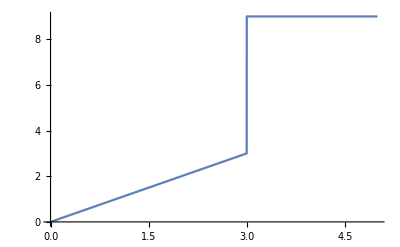

```mathematica
ClearAll[f, Test]
Test[y_] := y <= 3
f[x_?Test] := x
f[x_] := 9
Plot[f[x], {x, 0, 5}]
```

```mathematica
ClearAll[a]
a[n_] := n*a[n-1]
a[0] := 1
a[3]
Trace[a[3]]
```

6

{a[3],3 a[3-1],{{3-1,2},a[2],2 a[2-1],{{2-1,1},a[1],1 a[1-1],{{1-1,0},a[0],1},1 1,1},2 1,2},3 2,6}

```mathematica
?Trace
```

#### Table

```mathematica
Table[predmet, {10}]
```

{predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet}

```mathematica
?Table
```

```mathematica
Table[x^2, {x,10}]
Table[x^2, {x, 2, 10}]
Table[x^2, {x, 3, 10, 0.2}]
```

{1,4,9,16,25,36,49,64,81,100}

{4,9,16,25,36,49,64,81,100}

{9.,10.24,11.56,12.96,14.44,16.,17.64,19.36,21.16,23.04,25.,27.04,29.16,31.36,33.64,36.,38.44,40.96,43.56,46.24,49.,51.84,54.76,57.76,60.84,64.,67.24,70.56,73.96,77.44,81.,84.64,88.36,92.16,96.04,100.}

```mathematica
ClearAll[a, n, i]
a[n_Integer] := n*a[n-1]
a[0] := 1
Table[a[i], {i, 100}];
Timing[Table[a[i], {i,100}]][[1]]
```

0.015625

```mathematica
?Timing
```

Timing[[1]]	=	Čas potřebný pro výpočet